```mathematica
pGauss={0.9924842530760968,0.9968265953644178,0.9980472767460579,0.9985860253229631,0.9988899322741573,0.9990877714044637,0.9992276288334452,0.9993312437585575};
pSharp={0.9924340802444324,0.9968633324331205,0.9980646276660015,0.9985865372606662,0.9988940909311378,0.9990867207468865,0.9992270372156965,0.9993308620533231};
TValues={1,2,3,4,5,6,7,8};
```

```mathematica
pExp={0.9909337427465923,0.9959417448431935,0.9974524802381469,0.9981612693682584,0.9985648349484741,0.998818340440565};
numSteps=5;Ω=1;
TMin = 0.4/Ω;  TMax = 4/Ω; TStepSize = Abs[TMin-TMax]/numSteps;
TValuesExp = Table[T,{T,TMin,TMax,TStepSize}]
```

{0.4,1.12,1.84,2.56,3.28,4.}

```mathematica
dataGauss=Transpose[{TValues,pGauss}]
dataSharp=Transpose[{TValues,pSharp}]
dataExp=Transpose[{TValuesExp,pExp}]
```

{{1,0.992484},{2,0.996827},{3,0.998047},{4,0.998586},{5,0.99889},{6,0.999088},{7,0.999228},{8,0.999331}}

{{1,0.992434},{2,0.996863},{3,0.998065},{4,0.998587},{5,0.998894},{6,0.999087},{7,0.999227},{8,0.999331}}

{{0.4,0.990934},{1.12,0.995942},{1.84,0.997452},{2.56,0.998161},{3.28,0.998565},{4.,0.998818}}

### actually this exp data used a different r value and thus this comparison is noooooot real :(

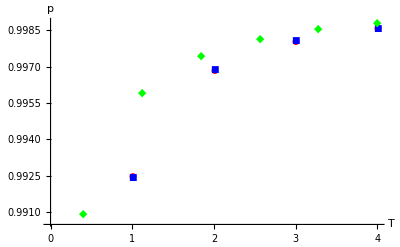

```mathematica
ListPlot[{dataGauss[[All]][[1;;4]],dataSharp[[All]][[1;;4]],dataExp},
AxesLabel->{T Ω,p},
PlotStyle->{Red,Blue,Green,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

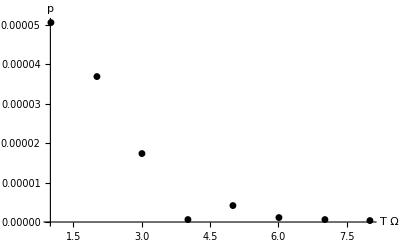

```mathematica
ListPlot[{Transpose[{TValues,Abs[pGauss-pSharp]/pSharp}]},
AxesLabel->{T Ω,p},
PlotStyle->{Red,Blue,Green,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```